# Wireless Communication Network

## Lab 5 - MIMO & 2 Flow Assigment

Chen Mishali (204377915) & Idan Vaknin

General:

```mathematica
Clear["Global`*"] (*Clear All Args*)

t=5;  (*Transmission Antennas*)
K=30;(*Users*)
P=5;  (*Transmission Power*)
μ=0; (*Expected Value*)
σ=1; (*Variance*)
Repeats=5000;(*Repeats each simulations 5000 times*)
funcs={ComplexGaussianChannel,ChaoticChannel,CorrelativeChannel}; (*channels names*)
```

Define 3 types of channels
In this part we define 3 types of channels which assume that users are i.i.d:
a. An i.i.d complex Gaussian channel equally distributed – the connection between each receiving
antenna and each of the t transmitting antennas is described by a vector of the length t so that
each entry in the vector has a real and a complex parts Gaussian distributed with an expected
value of 0 and a variance of 1 and is i.i.d to all other entries.

```mathematica
ComplexGaussianChannel[]:=Table[RandomVariate[NormalDistribution[μ,σ]] + ⅈ*RandomVariate[NormalDistribution[μ,σ]],{i,1,t},{j,1,K}]
```

b. A chaotic channel model – each channel is characterized complex Gaussian distribution with a
random expected value uniformly distributed U[0,1] and a variance uniformly distributed U[0,3].
The parameters for each channel’s distribution are only drawn once.

```mathematica
ChaoticChannel[]:=Module[{μ,σ},
μ = RandomVariate[UniformDistribution[{0,1}]];
σ = RandomVariate[UniformDistribution[{0,3}]];
ConstantArray[RandomVariate[NormalDistribution[μ,σ]] + ⅈ*RandomVariate[NormalDistribution[μ,σ]],{t,K}]]
```

c. A complete correlative channel – all the antennas have the same randomly drawn complex
Gaussian distribution with an expected value of 0 and a variance of 1. The is only drawn once.

```mathematica
CorrelativeChannel[]:= ConstantArray[RandomVariate[NormalDistribution[μ,σ]] + ⅈ*RandomVariate[NormalDistribution[μ,σ]],{t,K}];
```

Selecting Users (Multi Users)
1. Assuming there are K users, what is the number of maximal users the station can
simultaneously transmit to using Zero-Forcing Beam Forming (ZFBF) encoding for each of the
channels?

We know that there is T antennas, K users and we are using Zero-forcing method to transfer the signal. The purpose of Beamforming (ZF) precoding is to concentrate  the signal energy to the specific user while minimize inter-user interference  to other users. In class we studied that the k user received signal strength equal to: 
Y_k= ∑_(j≠k)^ √P_j H_k V_j S_j +√P_k h_k V_k S_k  
while V_k depends on the number of antennas.
If we want to eliminate all users interference the  maximal number of users must equal to T, so we get K=T is the best scenario.

Assuming there are K=30 users and the transmission power is P=5W. Conduct simulations that
receives the number of antennas at the transmitter t as an input. Repeat each simulation 5,000 times
and display the PDF of the total rates per transmission for each of the defined channels above.
Repeat for each of the following cases:
2. The base station chooses a single user at random and transmits to it at maximum power.

```mathematica
Simulation[channel_]:=Module[{rand, user, rate},
rand = RandomInteger[{1,K}];
user=channel[][[All,rand]];
rate = Log2[1+P Norm[user]^2]
]
```

```mathematica
PlotResults[channel_,Simulation_]:=(data=Table[Simulation[channel],Repeats];
Histogram[data,{0, 15, 0.015}, "PDF", AxesLabel -> {"Rate", "PDF"}, PlotLabel -> channel,PlotTheme->"Detailed"])
```

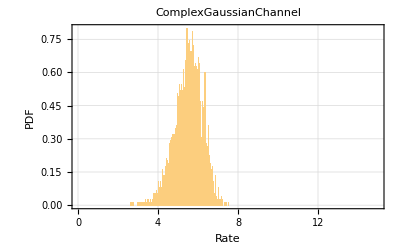
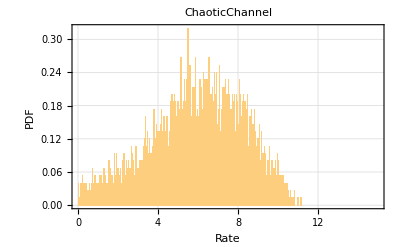
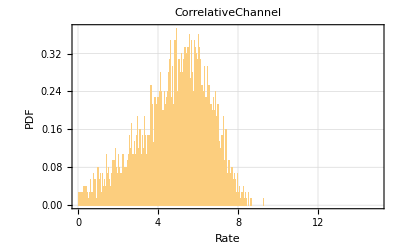

```mathematica
Table[PlotResults[funcs[[i]],Simulation],{i,3}]
```

3. The base station chooses to transmit to a single user with the strongest channel (the user with
the highest norm) and transmits to it at maximum power.

```mathematica
MaxPowerSimulation[channel_]:=Module[{rand, user, rate},
users=Table[channel[][[All,x]],{x,K}];
MaxNorm=Max[Table[Norm[users[[u]]],{u,K}]];
rate = N[Log2[1+P MaxNorm^2]]
]
```

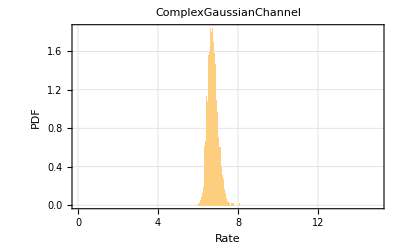
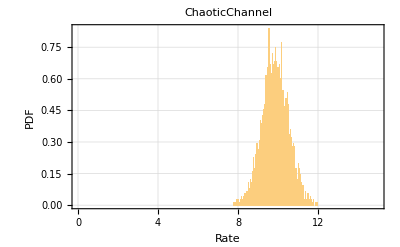
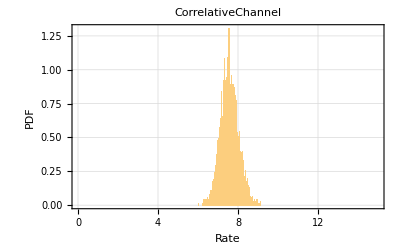

```mathematica
Table[PlotResults[funcs[[i]],MaxPowerSimulation],{i,3}]
```